```mathematica
(* Interpolate data and obtain E *)


mFileNameBaseEven = "/Users/zelimir/Work/Physics-Thesis/thesis-2/FortranCode/Files-ground-state-Even/Eigenvalues-Even-M-R=";
lFileNameBaseEven ="/Users/zelimir/Work/Physics-Thesis/thesis-2/FortranCode/Files-ground-state-Even/Eigenvalues-Even-L-R=";

mFileNameBaseOdd = "/Users/zelimir/Work/Physics-Thesis/thesis-2/FortranCode/Files-ground-state-Odd/Eigenvalues-Odd-M-R=";
lFileNameBaseOdd ="/Users/zelimir/Work/Physics-Thesis/thesis2/FortranCode/Files-ground-state-Odd/Eigenvalues=Odd-L-R=";

allRs = Table[0.1+i*0.1,{i,0,9}];

allRs = Join[allRs, Table[1+.5*i,{i,1,15}]]

(* In Eigenvalues table, 
	1^st index = integer (1,2..) corresponding to the index in radii table,
	2^nd index = Table (M or L ),
    3^rd index = row in a table,
    4^th index = element 

	ein parameter = eigenvalue order, 1 = lowest, etc...
*)
ImportEigenvalues[radii_, mEigenvalueOrder_, lEigenvalueOrder_, mFileNameBase_,lFileNameBase_]:=Module[ {rrs=radii, mEigenNum =mEigenvalueOrder, lEigenNum=lEigenvalueOrder, r,mFile, lFile, mEigenvalues,lEigenvalues, eigenValues, fname, len},

eigenValues = Table[0,{i,1,Length[rrs]}];

Do[
r=ToString[NumberForm[rrs[[i]],{3,1}]];

fname = mFileNameBase <> r <> ".dat";

mFile = Import[fname, "Table"];

len = Length[mFile];

mEigenvalues = Table[0,{i,1,len}, {j,1,2}];
Do[
mEigenvalues[[i]][[1]] = mFile[[i]][[1]];
mEigenvalues[[i]][[2]] = mFile[[i]][[mEigenNum+1]],
{i, 1,len}
];

fname = lFileNameBase <> r <> ".dat";

lFile = Import[fname,"Table"];

len = Length[lFile];

lEigenvalues = Table[0,{i,1,len}, {j,1,2}];
Do[
lEigenvalues[[i]][[1]] = lFile[[i]][[1]];
lEigenvalues[[i]][[2]] = lFile[[i]][[lEigenNum+1]],
{i, 1, len}
];

eigenValues[[i]] = {mEigenvalues,lEigenvalues},
{i,1,Length[radii]}
];

Return[eigenValues];

]

(*11 = 1sg+, 12 = 2sg+*)
(* In eigenvalues return, 
	1^st index = integer (1,2..) corresponding to the index in radii table,
	2^nd index = Table (M or L ),
    3^rd index = row in a table,
    4^th index = element [[1]] = p, [[2]] = eigenValue
*)
eigenValuesEven = ImportEigenvalues[radii,1,1,mFileNameBaseEven,lFileNameBaseEven];

eigenValuesOdd = ImportEigenvalues[radii,1,1,mFileNameBaseOdd,lFileNameBaseOdd];


calcPandA[distance_,elementIndex_,eigenValuesForR_]:=Module[{ r=distance,ei = elementIndex[[1]],evr =eigenValuesForR, mFunc, lFunc, p,a, energy, al, am},

mFunc = Interpolation[ evr[[ei]][[1]], InterpolationOrder->2] ; 
lFunc  = Interpolation[evr[[ei]][[2]],InterpolationOrder->2] ;

  (* value of p *)
If[r≥1,
	p =x /. FindRoot[mFunc[x] == lFunc[x],{x,r/2.}, WorkingPrecision->60],
p =x /. FindRoot[mFunc[x] == lFunc[x],{x,r}, WorkingPrecision->60]];

(* value of A *)
am= N[mFunc[p],60];
al = N[mFunc[p],60];

If[Abs[am - al] > .01, Print["ERROR Abs[am - al] = ",Abs[am - al]];Print["R = ",r]];
energy = N[-2(p/r)^2];

Return[{r,p,am,energy,energy  + 1/r,al}]
];
 

outValsEven:= MapIndexed[calcPandA[#1,#2,eigenValuesEven] &,{1}];
```

```mathematica
outValsOdd:= MapIndexed[calcPandA[#1,#2,eigenValuesOdd] &,{.6}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 60. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

(R | p | Am | E | E+1/r | Al
0.2 | 0.200200000000000540720115098471735768885107238514401228361961 | 0.0200902 | -2.004 | 2.996 | 0.0200902
0.4 | 0.648299122494951759923062624269802960513568110478841544483276 | 0.215659 | -5.25365 | -2.75365 | 0.215659
0.6 | 0.896854649548887178182077191768475350991900564914804938609905 | 0.422304 | -4.4686 | -2.80193 | 0.422304
0.8 | 1.12148762622110962872600314654131459412953182706743169433367 | 0.677779 | -3.93042 | -2.68042 | 0.677779
1. | 1.33110236019495414455652797262353173209228429998973730619132 | 0.982007 | -3.54367 | -2.54367 | 0.982007
1.2 | 1.53120581203895199918930377068504861406161876059839332953061 | 1.33809 | -3.25638 | -2.42304 | 1.33809
1.4 | 1.72549305403833275653337371068561464819726377403069639271387 | 1.75074 | -3.03809 | -2.3238 | 1.75074
1.6 | 1.91655474043762490090793084859594797888487685533741300414334 | 2.22543 | -2.86967 | -2.24467 | 2.22543
1.8 | 2.10622232133763111527915442968117222666682733197337368258323 | 2.76777 | -2.73838 | -2.18282 | 2.76777
2. | 2.29575534454662254130543137536271662034726154385470137109237 | 3.38297 | -2.63525 | -2.13525 | 3.38297
2.2 | 2.48596266865729929522993061675890439216094908556238529673266 | 4.07548 | -2.55372 | -2.09918 | 4.07548
2.4 | 2.67729974649767898082302641525884247182878236925298795489965 | 4.84875 | -2.48887 | -2.0722 | 4.84875
2.6 | 2.86995764142967386800365774545817929753304904372853550986733 | 5.70516 | -2.43688 | -2.05227 | 5.70516
2.8 | 3.0639450202072447340797627570560846249749468627658708502759 | 6.64611 | -2.39484 | -2.03769 | 6.64611
3. | 3.25915870958619368072598275663763612035091715985992344081779 | 7.67222 | -2.36047 | -2.02714 | 7.67222
3.2 | 3.45543886688592949114580098257398724575737154521260473261091 | 8.78351 | -2.33204 | -2.01954 | 8.78351
3.4 | 3.65260767329550416187847687026899831440237866726576508201105 | 9.97968 | -2.30823 | -2.01411 | 9.97968
3.6 | 3.85049336938190352837679569690240477728123822547810602080938 | 11.2602 | -2.28801 | -2.01023 | 11.2602
3.8 | 4.04894299902209690367614437997824392988038136335939310301571 | 12.6244 | -2.27063 | -2.00747 | 12.6244
4. | 4.24782738134196674968742185820992597732268416778164881887718 | 14.0717 | -2.2555 | -2.0055 | 14.0717
4.2 | 4.44704145383317716860242955681644869136981412793829804286376 | 15.6016 | -2.2422 | -2.0041 | 15.6016
4.4 | 4.64650208377716013406429943099825767269086067563513730822634 | 17.2136 | -2.23037 | -2.0031 | 17.2136
4.6 | 4.84614485395252797255662211035203996295495088020288676489145 | 18.9072 | -2.21977 | -2.00237 | 18.9072
4.8 | 5.04592068468714310317281067497859154144500212063313865010516 | 20.6821 | -2.21018 | -2.00185 | 20.6821
5. | 5.24579264890178798658842869253763696937853389101746870437637 | 22.538 | -2.20147 | -2.00147 | 22.538
5.5 | 5.74573026040406427929767645520131233438654305700765689834952 | 27.5309 | -2.18271 | -2.00089 | 27.5309
6. | 6.24585151428767837382132096209860392613949509055260023160372 | 33.0265 | -2.16726 | -2.00059 | 33.0265
6.5 | 6.74603763309184616956784066423945454252404652084607050710474 | 39.0236 | -2.15427 | -2.00043 | 39.0236
7. | 7.24623803812183696747275726808745408263207066212885365530383 | 45.5215 | -2.14318 | -2.00033 | 45.5215
7.5 | 7.74643255097550624010250351208379105387045668318357627413207 | 52.5198 | -2.13359 | -2.00026 | 52.5198
8. | 8.24661409530090404946618863407708403063991337011984228411166 | 60.0184 | -2.12521 | -2.00021 | 60.0184
8.5 | 8.74678102267203149147185674097032428135232648425123613833421 | 68.0173 | -2.11782 | -2.00017 | 68.0173
9. | 9.24693378553570760647385572620729440116024103885061791174849 | 76.5162 | -2.11125 | -2.00014 | 76.5162
9.5 | 9.74707355359210925759034014626172415169172696253196974680577 | 85.5153 | -2.10538 | -2.00012 | 85.5153
10. | 10.247201649915195651517687774338764877071511916889479110182 | 95.0145 | -2.1001 | -2.0001 | 95.0145
10.5 | 10.7473193436148102974873319804927870373554492193501896935004 | 105.014 | -2.09533 | -2.00009 | 105.014
11. | 11.247427780710093941920088203045914857928420883467768298658 | 115.513 | -2.09099 | -2.00008 | 115.513
11.5 | 11.7475279627458582073751029982248477418342010822025560897557 | 126.513 | -2.08702 | -2.00007 | 126.513
12. | 12.2476207742491461198642589578695976895042866127862403099703 | 138.012 | -2.08339 | -2.00006 | 138.012
12.5 | 12.7477069668870414974900651872487097111320987876184607223706 | 150.012 | -2.08005 | -2.00005 | 150.012
13. | 13.2477872341494424355173154661013827111793520822758310663675 | 162.511 | -2.07697 | -2.00005 | 162.511
13.5 | 13.747862136619372804853926108448425813186130237889687188968 | 175.511 | -2.07411 | -2.00004 | 175.511
14. | 14.2479321929686787441491590698639373989697998026814450639655 | 189.01 | -2.07147 | -2.00004 | 189.01
14.5 | 14.7479978537373774285392812257256342960960372897010611792368 | 203.01 | -2.069 | -2.00003 | 203.01
15. | 15.2480595081005063619114649931540613655291722288494943304826 | 217.51 | -2.0667 | -2.00003 | 217.51
15.5 | 15.748117518541081079522478430759120295748138018167294749361 | 232.509 | -2.06454 | -2.00003 | 232.509
16. | 16.2481721797617275402104101718247723208354403606366520018686 | 248.009 | -2.06252 | -2.00002 | 248.009
16.5 | 16.7482237909123159547811487931586400627665605982900137727043 | 264.009 | -2.06063 | -2.00002 | 264.009
17. | 17.248272583112855460063766052285174303642473905644715015395 | 280.508 | -2.05884 | -2.00002 | 280.508
17.5 | 17.7483187829982927285813729876483411964543489127835148665688 | 297.508 | -2.05716 | -2.00002 | 297.508
18. | 18.2483625902237266103928060233937320727191248721202505855832 | 315.008 | -2.05557 | -2.00002 | 315.008
18.5 | 18.7484041853277278829133692047175535765613841734868259618903 | 333.008 | -2.05407 | -2.00002 | 333.008
19. | 19.2484437363240609254978607925652787026191204285800525703012 | 351.508 | -2.05265 | -2.00001 | 351.508
19.5 | 19.7484813803432523083247266458129993235338825177370439130292 | 370.507 | -2.0513 | -2.00001 | 370.507
20. | 20.2485172528534136964753179003462893631859737467854325893013 | 390.007 | -2.05001 | -2.00001 | 390.007
20.5 | 20.7485514794981388099117013175300249937500898572628514037838 | 410.007 | -2.04879 | -2.00001 | 410.007
21. | 21.2485841746673194010955527736375293332019599252657310328729 | 430.507 | -2.04763 | -2.00001 | 430.507
21.5 | 21.7486154182627334873660972073273186745318922781283667994279 | 451.507 | -2.04652 | -2.00001 | 451.507
22. | 22.2486453289859668627789064522045910762109917887597351077167 | 473.006 | -2.04546 | -2.00001 | 473.006
22.5 | 22.7486739735233165968674099565771314581876605044770661007147 | 495.006 | -2.04445 | -2.00001 | 495.006
23. | 23.2487014405225633861153630792241834760452939080929884870954 | 517.506 | -2.04349 | -2.00001 | 517.506
23.5 | 23.7487277919168503116906201606128630163091365723985895833104 | 540.506 | -2.04256 | -2.00001 | 540.506
24. | 24.248753105376343675075597054412070685992761573356848916333 | 564.006 | -2.04167 | -2.00001 | 564.006
24.5 | 24.7487774206572370869628044226744112767559597881701573436619 | 588.006 | -2.04082 | -2.00001 | 588.006
25. | 25.2488008248345254668967128735563383063122818738725295154013 | 612.506 | -2.04001 | -2.00001 | 612.506)

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 60. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 60. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 60. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

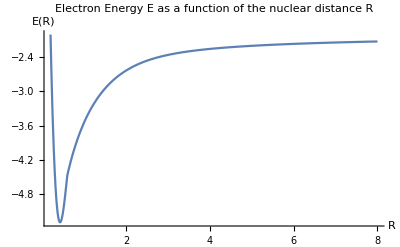

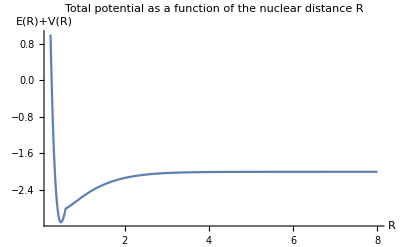

```mathematica
Prepend[outValsEven,{"R","p", "Am","E","E+1/r","Al"}] // MatrixForm
 Prepend[outValsOdd,{"R","p","Am","E","E+1/r","Al"}] // MatrixForm;


(* R = 0, E = 8, from the Yang, Guo, Chan paper *)

vRepulsive[r_]:=If[r ==0,1/(.000001),1/r];

outRsTableEven =outValsEven[[All,{1,4}]];
outRsTableOdd = outValsOdd[[All,{1,4}]] ;

outRsFuncEven = outRsTableEven //Interpolation;
outRsFuncOdd= outRsTableOdd //Interpolation;

Plot[outRsFuncEven[r]  ,{r,0.2,8}, AxesOrigin->{0,0}, PlotRange->{1,-6}, AxesLabel->{"R", "E(R)"},
PlotLabel->"Electron Energy E as a function of the nuclear distance R"]

Plot[outRsFuncEven[r] +1/r,{r,0.2,8}, AxesOrigin->{0,0}, PlotRange->{1,-6}, AxesLabel->{"R", "E(R)+V(R)"}, PlotLabel->"Total potential as a function of the nuclear distance R"]


(*Plot[outRsFuncOdd[r] ,{r,0.2,8}, AxesOrigin->{0,0}, PlotRange->{1,-4}]*)
```